```mathematica
(*Equations A.6 and A.7  n=2 going towards 3 .... as rho -> 0 the dominant solution seems to be n=3 *)
Clear[mh,dmh,mw,i]
mh:=√2;
dmh:=0;     (*dmh^2 = +0.032949999999 has no solution,						 dmh^2 = +0.032950000000 has an oscillon which is dmh=0.181521348607*)
(*-0.0395105 has no solution,  but -0.0395106 does which is dmh=0.198772*)
mw:=mh/2;
r0:=5.7;    (*a[r0]==6.3, a'[r0]==-3, b[r0]==12.0, b'[r0]==-8.6*)  
ar0:=6.3;
dadrr0:=-3; 
br0:=14(*12.5 this was primarily measured*); 
dbdrr0:=-9.1(*-8.6 was primarily measured*);
rtarget:=0.01(*0.07*);    (*a[rtarget]==0.8, b[rtarget]==-0.05*)
artarget:=0.21(*0.8*); 
brtarget:=0.01(*-0.06*);
rtest:=0.7;          (*a[rtest]==8.05, b[rtest]==-6.3*)
artest:=8.05; 
brtest:=-6.3;
```

```mathematica
√0.032950000000
√0.0395105
```

0.181521

0.198772

```mathematica
ⅇ^0.181521
```

1.19904

```mathematica
sol = NDSolve[{a''[r] -(mh^2+dmh)*a[r]+(b[r])^2/(4*r)== 0,b''[r]-mw^2*b[r]-(2*b[r])/r^2+mw^2/r*a[r]*b[r]==0,a[r0]==ar0,a[rtarget]==0.8,b[r0]==br0,b[rtarget]==brtarget},{a,b},r, Method->{"Shooting","StartingInitialConditions"->{a[r0]==ar0,b[r0]==br0,a'[r0]==dadrr0,b'[r0]==dbdrr0}},MaxSteps->50000];
Abs[Evaluate[a[rtest]/.sol]-artest]
Abs[Evaluate[b[rtest]/.sol]/(√2)-brtest/(√2)]
Abs[Evaluate[a[rtarget]/.sol]-artarget]
Abs[Evaluate[b[rtarget]/.sol]/(√2)-brtarget/(√2)]
```

NDSolve::ndsz: At r == 2.6761, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At r == 1.86819, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At r == 1.2276, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: "ndsz" will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

NDSolve::berr: There are significant errors {1.19582, 9.84516, -0.00898934, 1.60169} in the boundary value residuals.  Returning the best solution found.

{11.2234}

{16.0923}

{10.4363}

{1.1276}

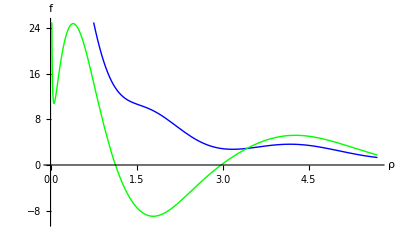

```mathematica
Plot[{Evaluate[a[r] /. sol]/r,Evaluate[b[r] /. sol]/(√2*r)}, {r,0.01,5.7},PlotStyle->{Blue,Green},AxesLabel->{ρ,f},AxesOrigin->{0,0},PlotRange->{-10,25}]
(*a/r is blue   b/r is green*)
```

```mathematica
Do[Print[Evaluate[b[i] /. sol]/(√2*i)],{i,0.07,5.7,0.05}]
```

```mathematica
(*Arhiv

a[7.1]==2.1,a[0.4]==27.8,b[0.4]==-1.6,b[7.1]==6.4},{a,b},r, Method->{"Shooting","StartingInitialConditions"->{a[7.1]==2.1,b[7.1]==6.4,a'[7.1]==-0.1,b'[7.1]==-0.3}}];




a[7.07]==2.83,a[1.41]==10.72,b[7.07]==7.07,b[1.41]==-10.01},{a,b},r, Method->{"Shooting","StartingInitialConditions"->{a[7.07]==2.83,b[7.07]==7.07,a'[7.07]==-0.2,b'[7.07]==-0.4}}];    best so far*)
```